```mathematica
C2=100*10^(-9);
C1=2*C2;
R1=R2=1000
c = N[1/Sqrt[2]/Pi/C1/R1]
```

1000

1125.4

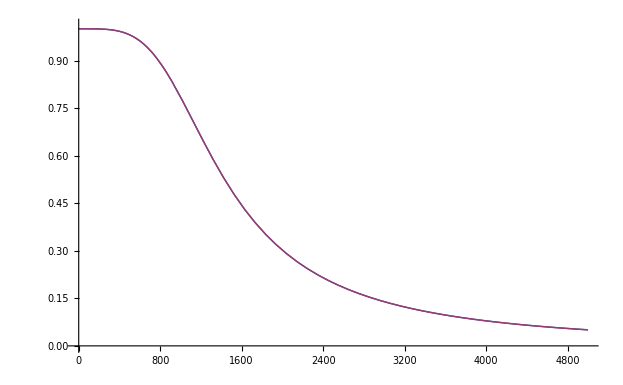

```mathematica
Lambda[f_]:=1/(1+C2*(R1+R2)*(2*Pi*I*f)+R1*R2*C1*C2*(2*Pi*I*f)^2)
AbsLambda[f_]:=Sqrt[1/(1+(f/c)^4)]
Plot[{Abs[Lambda[f]],AbsLambda[f]},{f,0,5000},PlotRange->{0,1.01}]
```

```mathematica
β=Exp[3*Pi/4*I]
Expand[FullSimplify[Expand[(s/2/Pi/c-β)*(s/2/Pi/c-Conjugate[β])]]]
```

ⅇ^((3 ⅈ π)/4)

1+s/(√2 c π)+s^2/(4 c^2 π^2)